```mathematica
SetDirectory[NotebookDirectory[]];
```

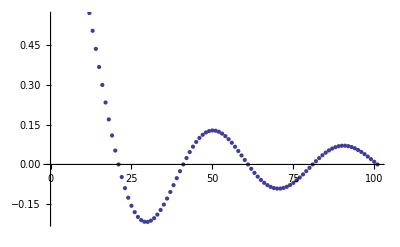

```mathematica
dat= Table[Sinc[-5π t/0.01],{t,0,0.01,0.0001}];
ListPlot[dat]
```

```mathematica
Export["waveform.csv",dat,"CSV"]
```

waveform.csv